```mathematica
Ln=4;
Co=2;
```

P(l<L,c) . FOR some reason I cannot get it to take the c-1th derivative. Well I can but it does not want to plot it, giving me an error message: “ref/message/D/dvar”

```mathematica
P1[l_,c_,p_]:=(1-p)^c/((c-1)!)*D[p^(l+c-1),{p,c-1}]
```

P(l=L,c)

```mathematica
P2[L_,c_,p_]:=1-(1-p)^c/((c-1)!)*D[p^(c-1)*(1-p^L)/(1-p),{p,c-1}]
```

For comparison P(l<L, c=1)

```mathematica
P11[l_,p_]:=(1-p)* p^l
```

P(l=L,c=1)

```mathematica
P21[L_,p_]:=p^L
```

Entropy c=1

```mathematica
EN1[L_,p_]:=-(Sum[P11[l,p]*Log[P11[l,p]],{l,0,L-1}]+p^L*Log[p^L])
```

P(l<L,c=2)

```mathematica
P12[l_,p_]:=(1-p)^2*(1+l) p^l
```

P(l=L,c=2)

```mathematica
P22[L_,p_]:=1-(1-p)^2*(-(L p^L)/(1-p)+(1-p^L)/(1-p)+(p (1-p^L))/(1-p)^2)
```

Entropy c=2

```mathematica
EN2[L_,p_]:=-(Sum[P12[l,p]*Log[P12[l,p]],{l,0,L-1}]+P22[L,p]*Log[P22[L,p]])
```

```mathematica
h[τ_]:=1/(1+1/τ)
T1=Evaluate@Table[P11[l,h[τ]],{l,0,Ln-1}]
T2=Evaluate@Table[P12[l,h[τ/2]],{l,0,Ln-1}];
```

{1-1/(1+1/τ),(1-1/(1+1/τ))/(1+1/τ),(1-1/(1+1/τ))/(1+1/τ)^2,(1-1/(1+1/τ))/(1+1/τ)^3}

```mathematica
T1={1-1/(1+1/τ),(1-1/(1+1/τ))/(1+1/τ),(1-1/(1+1/τ))/(1+1/τ)^2,(1-1/(1+1/τ))/(1+1/τ)^3}/τ
```

{(1-1/(1+1/τ))/τ,(1-1/(1+1/τ))/((1+1/τ) τ),(1-1/(1+1/τ))/((1+1/τ)^2 τ),(1-1/(1+1/τ))/((1+1/τ)^3 τ)}

Perfect Clock

```mathematica
PC[l_,τ_]:=(τ^l)/(l!)*ⅇ^-τ
PCM[L_,τ_]:=1-Sum[(τ^l)/(l!)*ⅇ^-τ,{l,0,L-1}]
ENP[L_,τ_]:=-(Sum[PC[l,τ]*Log[PC[l,τ]],{l,0,L-1}]+PCM[L,τ]*Log[PCM[L,τ]])
```

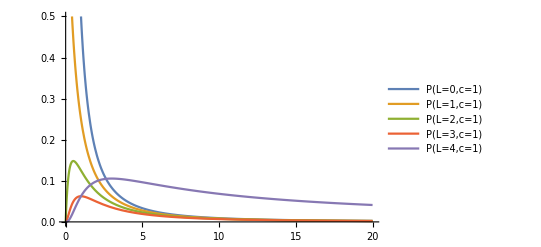

```mathematica
Plot[{T1,P21[Ln,h[τ]]/τ},{τ,0,20},PlotRange->{0,0.5}, PlotLegends->{"P(L=0,c=1)","P(L=1,c=1)","P(L=2,c=1)","P(L=3,c=1)","P(L=4,c=1)"}]
```

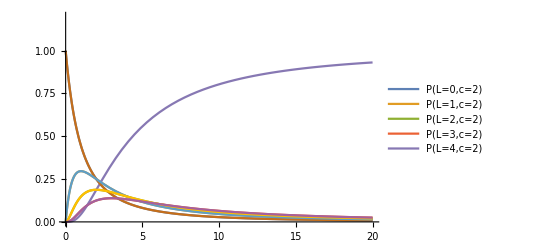

```mathematica
Plot[{T2,P22[Ln,h[τ/2]],T2},{τ,0,20}, PlotLegends->{"P(L=0,c=2)","P(L=1,c=2)","P(L=2,c=2)","P(L=3,c=2)","P(L=4,c=2)"}, PlotRange->{0,1.2}]
```

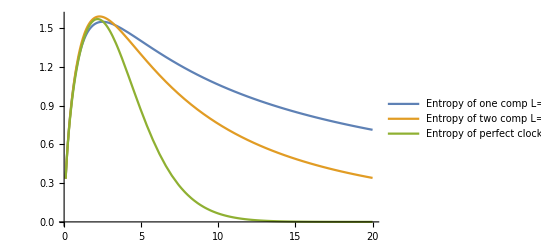

```mathematica
Plot[{EN1[Ln,h[τ]],EN2[Ln,h[τ/2]],ENP[Ln,τ]},{τ,0.1,20}, PlotLegends->{"Entropy of one comp L=4","Entropy of two comp L=4","Entropy of perfect clock L=4"}]
```

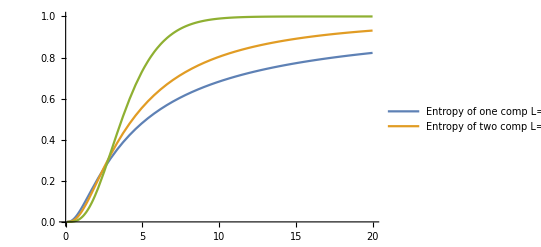

```mathematica
Plot[{P21[Ln,h[τ]],P22[Ln,h[τ/2]],PCM[Ln,τ]},{τ,0.1,20},PlotRange->{0,1}, PlotLegends->{"Entropy of one comp L=4","Entropy of two comp L=4"}]
```